```mathematica
Pattern[addition, {_,"+",_}]
```

addition:{_,+,_}

```mathematica
additionRules={__, "+",__}
```

{__,+,__}

```mathematica
MatchQ[{1, "+", 2}, additionRules]
```

True

```mathematica
commutativeGraph=[x, RelationGraph[commutativeAddition, {x,x}]][Range[100]](*Want to be able to define this functionally*)
```

```mathematica
commutativeGraph
```

commutativeGraph

```mathematica
MatchQ[1+2,2+1]
```

True

```mathematica
commutativeAddition[x_, y_]:=If[x+y==y+x, True, False]
```

```mathematica
algebra2PSet=Import["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\CK-12-Algebra-II-with-Trigonometry-Concepts_b_v78_eiy_s1.pdf", "Plaintext"]
```

1462420
 |  |  |  |

```mathematica
introAlgebraPSet=Import["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\scc_introductory_algebra_workbook_spring_2013.pdf", "Plaintext"];
```

```mathematica
calcPSet=Import["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\CalcI_Complete_Problems.pdf", "Plaintext"]
```

Import::general: Expected cross reference table

Import::general: Could not find document trailer

General::stop: Further output of Import::general will be suppressed during this calculation.

```mathematica
a1QsPEMDAS={ "What is 2+2", "2+3","What is 2+3", "What is 1+1", "What is 20+22", "What is 1+15+21", "What is 33+5+8", "Simplify (2-5)^2", "Simplify 2-5^2", "Simplify 10-7+1", "Simplify 10-(7+1)", "Simplify 24/(4-2)^3", "Simplify 4+5(1+12/6)^2", "Simplify (15-3)/(1+5)", "1+12", "10% of 11", "30+40", "15+12", "20% of 33" , "11+12", "What is 5% of 100?"};
```

```mathematica
a1QsFractions={"express 3 2/7 as an improper fraction", "express 12 1/3 as an improper fraction", "Express 42/5 as a mixed number", "Express 53/9 as a mixed number", "write 3/18 in simplest form", "write 42/54 in simplest form" "What is 3 2/7 as an improper fraction","What is 12 1/3 as an improper fraction","What is 42/5 as a mixed number","What is 53/9 as a mixed number","What is 3/18 in simplest form","What is 42/54 in simplest form"}
```

{express 3 2/7 as an improper fraction,express 12 1/3 as an improper fraction,Express 42/5 as a mixed number,Express 53/9 as a mixed number,write 3/18 in simplest form,What is 3 2/7 as an improper fraction write 42/54 in simplest form,What is 12 1/3 as an improper fraction,What is 42/5 as a mixed number,What is 53/9 as a mixed number,What is 3/18 in simplest form,What is 42/54 in simplest form}

```mathematica
{"express 3 2/7 as an improper fraction","express 12 1/3 as an improper fraction","Express 42/5 as a mixed number","Express 53/9 as a mixed number","write 3/18 in simplest form","write 42/54 in simplest form"}
a1QsOppFrac={"Multiply 24/3 and 27/8", "Multiply 8 and 3/24", "Add 1/2 and 1/3", "What is  24/3 * 27/8", "What is  8 * 3/24", "What is  1/2 + 1/3"};
a1QsAbsoluteVal={"What is the absolute value of -1?", "What is |1|", "What is |-30|"};
a1QsNegatice={"What is 3-(-2)?", "What is -3+4"};
a1QsIntovars={"Evaluate a^2-b^2 when a=5 and b=3", "Evaluate a-b^2 when a=4 and b=2", "Evaluate a^2+b when a=7 and b=1"}
```

{express 3 2/7 as an improper fraction,express 12 1/3 as an improper fraction,Express 42/5 as a mixed number,Express 53/9 as a mixed number,write 3/18 in simplest form,write 42/54 in simplest form}

{Evaluate a^2-b^2 when a=5 and b=3,Evaluate a-b^2 when a=4 and b=2,Evaluate a^2+b when a=7 and b=1}

```mathematica
{"express 3 2/7 as an improper fraction","express 12 1/3 as an improper fraction","Express 42/5 as a mixed number","Express 53/9 as a mixed number","write 3/18 in simplest form","write 42/54 in simplest form", }
```

{express 3 2/7 as an improper fraction,express 12 1/3 as an improper fraction,Express 42/5 as a mixed number,Express 53/9 as a mixed number,write 3/18 in simplest form,write 42/54 in simplest form,Null}

```mathematica
a1QsCombineLikeTerms={"Combine like terms of 3a-6a+10a-a", "Combine the like terms of 5x-10y+6z-3x", "Combine like terms of 3n-5n^2+6n-10+2n^2"};
```

```mathematica
a1QsDistrbutive={"5(2x+4)", "-3(x^2-2x+7)", "-(5x^4-8)"};
```

```mathematica
a1QsSolving={"8x-2=22", "-x-2=12", "2/3 x+3 =15"} ;
```

```mathematica
a1QsPolynomials={"Factor 3x^2+4x+1", "Factor n^2+5n+6", "Factor a^2+3a+2"};
```

```mathematica
a1QsPercent={"A $750 watch is on sale for 15% off. Find the sale price.", "A salesman tells you that the $140 earrings are already marked 20% off. What
was the original price?", "Tommy’s grandma gave him a $50 gift card to Toys R Us for his birthday.
Sales tax is currently 9%. Determine the price of the most expensive toy Tommy can buy with
the $50 gift card.", "A salesman is paid a monthly salary of $2,300 plus 7% commission on his monthly sales.
Determine the amount of sales required for his total monthly income to be $3,000.", 
"What is 10% of 100", "What is 4% of 16?", "200% of 3", "What is 45+300+4", "30+30", "90+200", "1+5", "34+1", "10% of 11", "5% of 112", "41+2" };
```

```mathematica
algebra1Questions=Flatten[{a1QsAbsoluteVal, a1QsCombineLikeTerms, a1QsDistrbutive, a1QsFractions, a1QsIntovars, a1QsPEMDAS, a1QsSolving, a1QsOppFrac, a1QsPercent, a1QsNegatice}];
```

```mathematica
algebra2PSetList[[8503;;8510]]
```

Part::take: Cannot take positions 8503 through 8510 in algebra2PSetList.

algebra2PSetList⟦8503;;8510⟧

```mathematica
algebra2Qs={"What is the most specific subset of the real numbers that -7 is a part of?", "Plot 1.25, 2/3 and 2 on a number line", "Identify the property used in the equations below as distributive, inverse or associative", "Evaluate 2x^2-9 for x=-3",  "Expand (a+b)^3", "What is (a+b)^n (Hint: What theorem is this?)", "Solve 4x-9=11", "Solve 3(x-5)+4=10", "Solve 3(x-5)+4=10", "Solve 9(x-3)+4=10", "Solve (x-1/2)=(2x+3)","Solve 3|x-5|=12","Solve 8(x-5)+4=10","Solve (x^2-5)=20",  "Use the law of sines to find the missing side of this triangle", "What is the largest value for the missing side of this triangle", "What is sin(60)", "What is tan(30)", "Write 30 degrees in radians", "Write π/4 in degrees", "Is x=-8 a solution to 1/2x+6>3?",  "Solve and graph the solution to 2x-3<7", "Solve and graph the solution to |3x-1|≥10",  "How many miutes are in a day?", "Wrie the standard form of y=3/2 x+2", "Write slope intercept form for a slope of 2 and y-intercept of 12", "Find a perpedicular line of y=3x+2 with y intercept of the origin","What are the domain and range of the trigonometric functions?" , "Graph the inequality y<3x+4", "Find the equation of best fit for the below listed data", "Graph the parabola give by x^2+3x+2. Find the zeros, vertex and intercept", "What is the sum from 1 to 5 of a=10n+3", "What is the next term in the series ", "what is the sum of the geometric series from 1 to infinity of 9(1/10)^n?", "What are the discontiuities in the function y=(x+2)/(x+3x+2). Which are fundamental and which are removable?", "What is ln(1)?", "What are the domain and range of e^x and ln(x)", "sin(40)", "cos(45)", "tan(63)", "sin(121)", "sin(π/3)", "sin(π/5)", "cos(π/13)"};
```

```mathematica
calcQspcalc={"Evaluate f(x)=3-5x-2x^2 for the below values: f(0), f(x+h), f(6-t)", "Compute  the difrence quotient for the given function",  "Find the domain of (w^3-3w+1)/(12 w-7)","Find the inverse of f (x) = 6x +15", "Find inverse of W (x) =  (9 −11x)^(1/5)", "Find the exact value of cos(5 π/6) without using a calculator", "Find the exact value of sin(-4 π/3) without using a calculator", "Solve  4sin (3t ) = 2", "Solve 4sin (3t ) = 2 in [0, 4π/3], 2cos(x/3) +2^0.5 = 0 in [−7π ,7π }", "Solve 4y sec(7 y) = −21y", "Solve 3−14sin (12t + 7) =13", "Solve 3sec(4 − 9z) − 24 = 0", "Sketch the graph of f(x)=3^(1 + 2  x)", "Sketch the graph of h(x)=8+3e^(2  t - 4)",  "Determine ln(e^4)", "Combine 2 log_4x +5 log_4y - 1/2 log_4x" , "For the function W(x)=ln(1+x^4) and the point x=1, find the secants at point Q and the tangenet line", "For the function f(x)=(8-x^2)/(x^2-4), find the values at the below listed points and th limit as x aproaches 2",  , "For the function f(y)= sin(y)/y find the value at the below listed points and the limit as y approaches 0"};
```

```mathematica
calcQsderivs={"For the function f(x)=(8-x^2)/(x^2-4), use L'Hoptial's rule to find the limit as x aproaches 2",  "For the function (2-(t^2+3)^(1/2))/(t+1), L'Hoptial's rule to find the limit as x approaches -1", "Use the definition of the derivative to find the derivative of f(x)=6", "Use the definition of the derivative to find the derivative of V (t ) = 3−14t", 
 "Use the definition of the derivative to find the derivative of z(n)= (n+1)/(n+4)",
"Use the chain rule to find the derivative of Q(t)=(3t^3-4)^(1/2)", "Use the quotient rule to find the derivative of z(n)= (z+1)^(1/2)/(z+4)", 
"Find the deriviative of f (x) = 2cos(x) − 6sec(x) + 3", "Find the deriviative of g (z) =10 tan (z) − 2cot (z)", "Find the deriviative of  tan (w)sec(w)", "Find the deriviative of R(t)=(t+ tan(t))/(1+csc(t))", "Find the derivative of f(x)=2e^x-8^x", "Find the derivative of g(t)=4 log_3(t)-ln(t)", "Find the derivative of 2 cos(x)+arccos(x)" , "Find the derivative of x^2/y^3=1", "Find extrema of f(x)=12+6x^2-x^3", "Find extrema of g(w)=tan (w)sec(w)", "find the taylor expanision of g(w)=tan (w)sec(w) at w=π/4", "Find the MacLauren Expanision of z(n)= (z+1)^(1/2)/(z+4)", "Find the Derivative", "What is the Deriviative", "Evaluate the derivative", "Integral of ln(x) dx", "Integral of f(x)=x ln(x) from 0 to 10", "Integral of tan(x)", "Integral of (1+x)^(1/2)"};
```

```mathematica
calcQsIntegral={"Find ∫6x^5 −18x^2 + 7 dx", "Find ∫6x^5 dx −18x + 7", "Evaluate ∫z^6 + 4z^4 − z^2 dz" ,"Determine f (x) given that f'(x) = 6x^8 − 20x^4 + x^2 + 9", "Find ∫ 2cos (w) − sec(w) tan (w)dw", "Find ∫12 + csc(θ ) [sin (θ ) + csc(θ )] dθ",
"What is ∫6x^5 −18x^2 + 7 dx", "Find ∫6x^5 dx −18x + 7",
"What is the integral of sin(2x)?", "Find the area under the curve of |x| from -1 to 1", "What is the area under the curve sin^2x from 0 to π/2", "Find the integral", "What is the integral of x dx", "Derivative of f(x)=x^2", "Integral of x dx", "Integral of e^y dy", "Derivative of x^3", "Derivative of x", "Derivative of f(x)=20 ln(x)", "Derivative of x/(x+1)^2", "Derivative of x^n", "Derivative with respect to x", "Derivative of x^3"};
```

```mathematica
calcQs=Flatten[{calcQspcalc, calcQsIntegral, calcQsderivs}];
```

```mathematica
Clear[questionClassifier]
questionClassifier=Classify[<|"algebra 1"->algebra1Questions, "algebra 2"->algebra2Qs, "calc"->calcQs|> , Method->"NaiveBayes", PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
equivilentFraction[x_, y_, n_]:= n*x/y ;
turnOffEquivFrac[question_]:=MatchQ[question, {__, "Fraction",__,"implest form"}]
Function[question,MatchQ[question,{"Fraction",__,"implest form"}]]
allpoints[question_]:=MatchQ[question, {__, "all points", __}]
eitherPointfirst[a_, b_,c_, d_]:= {{"(",a, b, ")"},{"("c, d")"}}-> {{"("c, d")"},{"(",a, b, ")"}}
isPoint[answer_]:=MatchQ[answer, {"("__")"}]
commutative[a_,b_]:=a+b-> b+a
distributive[a_,b_, c_]:=a*(b+c)-> a*b+a*c
commutativemulti[a_, b_]:=a*b-> b*a;
associative[a_, b_, c_]:=a+(b+c)-> (a+b)+c;
associativemulti[a_, b_,c_]:=a*(b*c)-> (a*b)*c;
isMatrix[answer_]:=MatchQ[answer, MatrixForm]
```

Function[question,MatchQ[question,{Fraction,__,implest form}]]

Classify::bdfmt: Argument «1» should be a rule, a list of rules, or an association.

Classify::bdfmt: Argument … should be a rule, a list of rules, or an association.

ClassifierFunction[…]

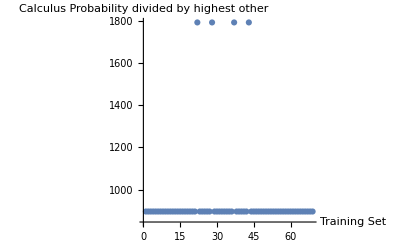

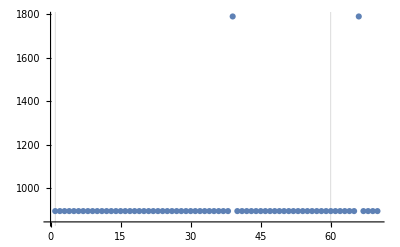

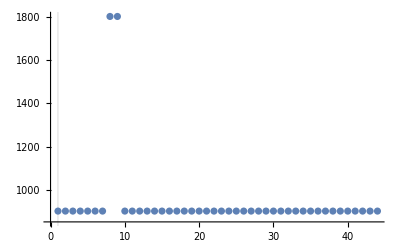

C:\Users\Silas Grossberndt\Documents\GitHub\WSS-Template\Final Project\Drafts\problem_sets\pset_trained_NaiveBayes.pdf

```mathematica
calctsetlist=questionClassifier[calcQs, {"Probability", "calc"}];

algebra1calctsetlist=questionClassifier[calcQs, {"Probability", "algebra 1"}];
algebra2calctsetlist=questionClassifier[calcQs, {"Probability", "algebra 2"}];
lp=ListPlot[#clac/#alge, AxesLabel->{"Training Set", "Calculus Probability divided by highest other"}]&@<|"clac"->calctsetlist, "alge"->algebra1calctsetlist, "alge2"-> algebra2calctsetlist|> 
a2tsetlist=questionClassifier[algebra2Qs, {"Probability", "algebra 2"}];

ca2tsetlist=questionClassifier[algebra2Qs, {"Probability", "calc"}];

a1a2tsetlist=questionClassifier[algebra2Qs, {"Probability", "algebra 1"}];
a1tsetlist=questionClassifier[algebra1Questions, {"Probability", "algebra 1"}];
ca1tsetlist=questionClassifier[algebra1Questions, {"Probability", "calc"}];
lp1=ListPlot[#alge1/#calc1, GridLines->{{0, 60, 1}}]&@<| "alge1"->a1tsetlist, "calc1"->ca1tsetlist|> 
lp2=ListPlot[#alge2/#calc1, GridLines->{{0, 60, 1}}]&@<| "alge2"->a2tsetlist, "calc1"->ca2tsetlist, "alge1"-> a1a2tsetlist|> 
Export["C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\pset_trained_NaiveBayes.pdf", {lp, lp1, lp2}]
```

```mathematica
"C:\\Users\\Silas Grossberndt\\Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\problem_sets\\pset_trained_.pdf"
```

C:\Users\Silas Grossberndt\Documents\GitHub\WSS-Template\Final Project\Drafts\problem_sets\pset_trained_.pdf

```mathematica
(*include the above graphs and the test functions to show infeasiability of doing the classifier*)

questionClassifier["Derivative of f(x)=x^2"]
questionClassifier["Integral of x dx"]

questionClassifier["What is 10% of 110", {"Probabilities"}]

questionClassifier["sin(π/5)"]
(*Need to add more training about sine to a2, derivative to calc*)

questionClassifier["35+3"]
questionClassifier["Derivative of x^6"]
ClassifierMeasurements[questionClassifier, <|"algebra 1"-> algebra1Questions,"algebra 2"-> algebra2Qs, "calc"-> calcQs|>, "Accuracy"]
```

calc

calc

{<|algebra 1→0.38172,algebra 2→0.241935,calc→0.376344|>}

algebra 2

algebra 1

algebra 1

1.